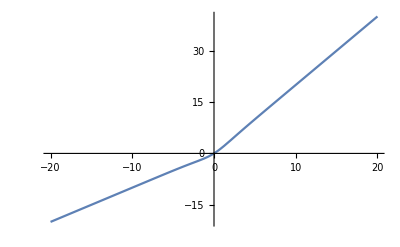

```mathematica
(* nonlinear, smooth approximation of a piecewise  linear objective function *) (*La prima parte è uguale al codice che mi hai inviato*)
p=1;
ftrue[x_]:=x(1+p(1+E^(-x))^(-1));
fmod[x_,a_,b_]:=x(1+b(1+E^(-a x))^(-1)); (*simplified form to have only two free parameters*)
Plot[ftrue[x],{x,-20,20}]
```

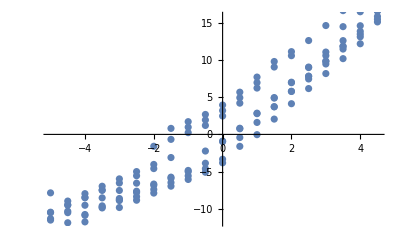

```mathematica
(* generate a sample from ftrue*)
nn=20;
ll=7;
xs = Table[xi-11,{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=4;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
ys=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];
plots = Table[
ListPlot[Table[{0.5i-5.5,ys[[i,2]][[j]]},{i,1,nn}],PlotRange->All],{j,1,ll}];
Show[plots]
```

```mathematica
(* ho definito la funzione di costo tenendo gli indici dei dati come variabili, in modo da valutare la funzione sulla singola coppia dato-label *)
lossol[a_,b_,i_,j_]:=
(ys[[i,2]][[j]]-fmod[ys[[i,1]],a,b])^2;
(*definizione di gradiente uguale alla tua; quando vado a valutarlo manualmente ritorna risultati sensati*)
gradol[a_,b_,i_,j_]:={D[lossol[x,y,i,j],x],D[lossol[x,y,i,j],y]}/.{x->a,y->b}
eta=0.0000001;
(*questa parte ritorna errore; ho scritto l'equazione ricorsiva per il due parametri della funzione, mi dice che l'array xs cannot be used as a part specification *)
(*recurrence=RecurrenceTable[{x[i+1,j+1],y[i+1,j+1]}=={x[i,j]-eta*Part[gradol[x[i,j],y[i,j],i,j],1] , y[i,j]-eta*Part[gradol[x[i,j],y[i,j],i,j],2]},{x[1,1]==0.5,y[1,1]==0.5},{i,1,nn},{j,1,ll}];*)
```

```mathematica
(*simuliamo le traiettorie continue definite dalla sde*)

loss[a_,b_]:=Sum[ Sum[(ys[[i,2]][[j]]-fmod[ys[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];
gradol[a_,b_]:={D[loss[x,y],x],D[loss[x,y],y]}/.{x->a,y->b}
proc=ItoProcess[{ⅆx[t]==Part[-gradol[x[t],y[t]],1]ⅆt+Sqrt[eta*2*loss[x[t],y[t]]] ⅆw1[t],ⅆy[t]==Part[-gradol[x[t],y[t]],2]ⅆt+Sqrt[eta*2*loss[x[t],y[t]]] ⅆw2[t]},{x[t],y[t]},{{x,y},{1,1}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}];

data=RandomFunction[proc,{0.,5.,0.1}]["Path"];
point = Table[{Part[Part[Part[data,n],2],1],Part[Part[Part[data,n],2],2]},{n,1,Part[Dimensions[data],1]}]
ListPlot[point,Joined->True,PlotStyle->PointSize[Small]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ItoProcess::simflr: Simulation of process ItoProcess[{{-∑_(i=1)^nn ∑_(j=1)^ll (2 fmod[«3»] («1»)^(«3»)[«3»]-2 Part[«2»] («1»)^(«3»)[«3»]),-∑_(i=1)^nn ∑_(j=1)^ll (2 fmod[«3»] («1»)^(«3»)[«3»]-2 Part[«2»] («1»)^(«3»)[«3»])},{{√2 √(eta Sum[«2»]),0},{0,√2 √(eta Sum[«2»])}},{x[t],y[t]}},{{x,y},{1,1}},{t,0}] failed.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ItoProcess::simflr: Simulation of process ItoProcess[{{-∑_(i=1)^nn ∑_(j=1)^ll (2 fmod[«3»] («1»)^(«3»)[«3»]-2 Part[«2»] («1»)^(«3»)[«3»]),-∑_(i=1)^nn ∑_(j=1)^ll (2 fmod[«3»] («1»)^(«3»)[«3»]-2 Part[«2»] («1»)^(«3»)[«3»])},{{√2 √(eta Sum[«2»]),0},{0,√2 √(eta Sum[«2»])}},{x[t],y[t]}},{{x,y},{1,1}},{t,0}] failed.

Part::partd: Part specification Path⟦2⟧ is longer than depth of object.

ItoProcess::simflr: Simulation of process ItoProcess[{{-∑_(i=1)^nn ∑_(j=1)^ll (2 fmod[«3»] («1»)^(«3»)[«3»]-2 Part[«2»] («1»)^(«3»)[«3»]),-∑_(i=1)^nn ∑_(j=1)^ll (2 fmod[«3»] («1»)^(«3»)[«3»]-2 Part[«2»] («1»)^(«3»)[«3»])},{{√2 √(eta Sum[«2»]),0},{0,√2 √(eta Sum[«2»])}},{x[t],y[t]}},{{x,y},{1,1}},{t,0}] failed.

General::stop: Further output of ItoProcess::simflr will be suppressed during this calculation.

Part::partd: Part specification Path⟦2⟧ is longer than depth of object.

{{Path,2}}

-Graphics-